```mathematica
path="/home/abduld/Dropbox/wbGPU/grader/dbReader/runtime";
```

```mathematica
lines=Import[path,"Text"];
lines=StringSplit[lines,"\n"];
```

```mathematica
ns=(ToExpression/@lines)/1.*^9;
```

```mathematica
Mean[ns]
```

2.49942

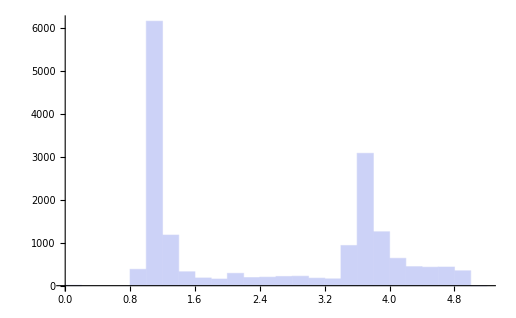

```mathematica
Histogram[ns]
```